# Catalan Numbers

Author Name

Abstract

## Section

XXXX:

## Catalan Numbers

```mathematica
CatalanNumber[Range[5]]
```

{1,2,5,14,42}

```mathematica
FindSequenceFunction[CatalanNumber[Range[5]],n]
```

CatalanNumber[n]

```mathematica
{{-Graphics-, AllBalancedGroupingSymbols}}[{"(",")"},3]
```

{((())),(()()),(())(),()(()),()()()}

```mathematica
{{-Graphics-, CatalanUnrank}}[4,#]&/@Range[0,CatalanNumber[4]-1]
```

{{0,0,0,0,1,1,1,1},{0,0,0,1,0,1,1,1},{0,0,0,1,1,0,1,1},{0,0,0,1,1,1,0,1},{0,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,1},{0,0,1,0,1,1,0,1},{0,0,1,1,0,0,1,1},{0,0,1,1,0,1,0,1},{0,1,0,0,0,1,1,1},{0,1,0,0,1,0,1,1},{0,1,0,0,1,1,0,1},{0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1}}

```mathematica
({{-Graphics-, CatalanUnrank}}[4,#]/.{0->-1})&/@Range[0,CatalanNumber[4]-1]
```

{{-1,-1,-1,-1,1,1,1,1},{-1,-1,-1,1,-1,1,1,1},{-1,-1,-1,1,1,-1,1,1},{-1,-1,-1,1,1,1,-1,1},{-1,-1,1,-1,-1,1,1,1},{-1,-1,1,-1,1,-1,1,1},{-1,-1,1,-1,1,1,-1,1},{-1,-1,1,1,-1,-1,1,1},{-1,-1,1,1,-1,1,-1,1},{-1,1,-1,-1,-1,1,1,1},{-1,1,-1,-1,1,-1,1,1},{-1,1,-1,-1,1,1,-1,1},{-1,1,-1,1,-1,-1,1,1},{-1,1,-1,1,-1,1,-1,1}}

```mathematica
Accumulate[({{-Graphics-, CatalanUnrank}}[4,#]/.{0->-1})]&/@Range[0,CatalanNumber[4]-1]
```

{{-1,-2,-3,-4,-3,-2,-1,0},{-1,-2,-3,-2,-3,-2,-1,0},{-1,-2,-3,-2,-1,-2,-1,0},{-1,-2,-3,-2,-1,0,-1,0},{-1,-2,-1,-2,-3,-2,-1,0},{-1,-2,-1,-2,-1,-2,-1,0},{-1,-2,-1,-2,-1,0,-1,0},{-1,-2,-1,0,-1,-2,-1,0},{-1,-2,-1,0,-1,0,-1,0},{-1,0,-1,-2,-3,-2,-1,0},{-1,0,-1,-2,-1,-2,-1,0},{-1,0,-1,-2,-1,0,-1,0},{-1,0,-1,0,-1,-2,-1,0},{-1,0,-1,0,-1,0,-1,0}}

```mathematica
{{-Graphics-, CatalanUnrank}}[4,1]
```

{0,0,0,1,0,1,1,1}

```mathematica
Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]]
```

{0,0,0,1,1,2,3,4}

```mathematica
Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}]
```

{-1,-2,-3,-2,-3,-2,-1,0}

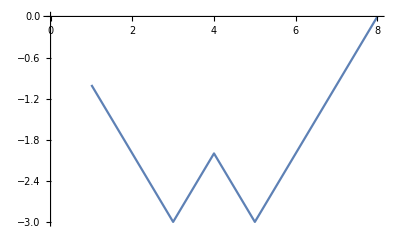

```mathematica
ListLinePlot[Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}]]
```

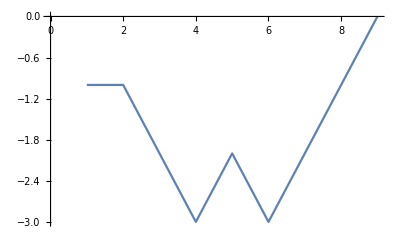

```mathematica
ListLinePlot[Join[{First[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}]},Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}]]]
```

```mathematica
Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}]
```

{-1,-2,-3,-2,-3,-2,-1,0}

```mathematica
Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}],0]
```

{0,-1,-2,-3,-2,-3,-2,-1,0}

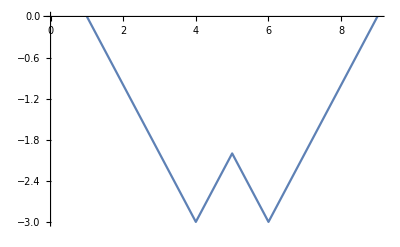

```mathematica
ListLinePlot[Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,1]/.{0->-1}],0]]
```

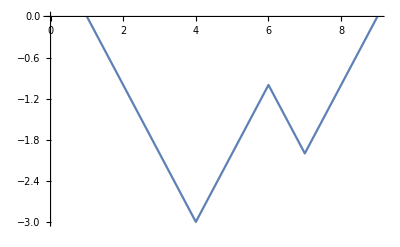

```mathematica
ListLinePlot[Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,2]/.{0->-1}],0]]
```

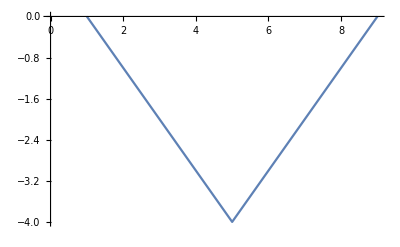
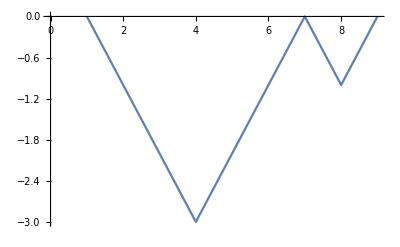
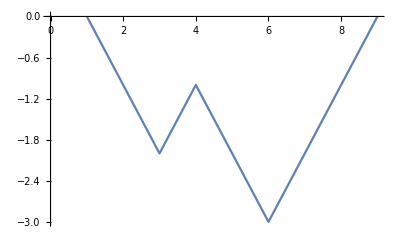
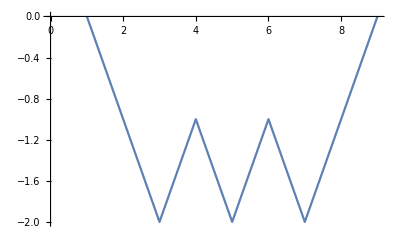
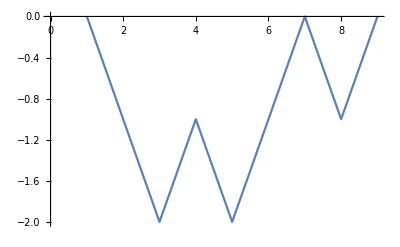
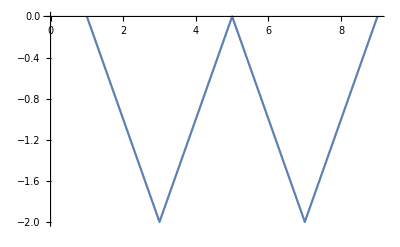
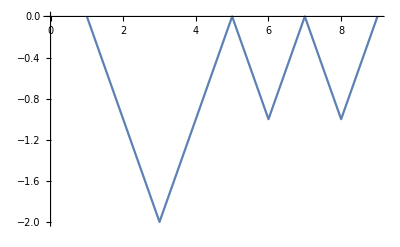
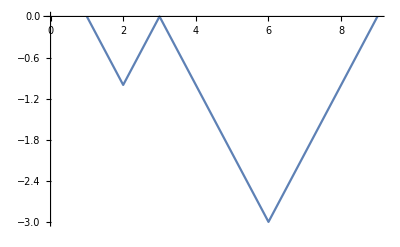
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,#]/.{0->-1}],0]]&/@Range[0,CatalanNumber[4]-1]
```

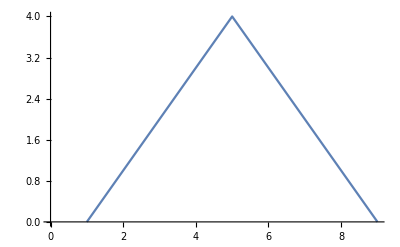
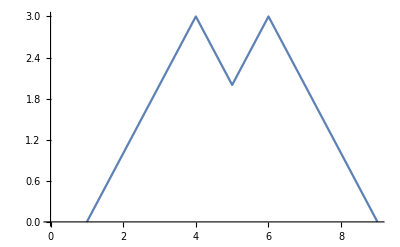
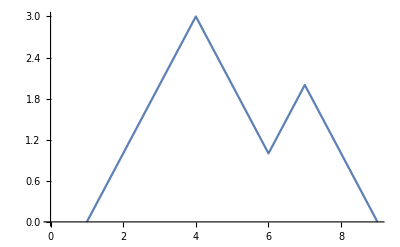
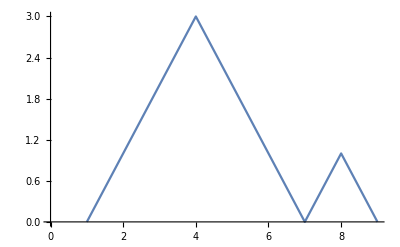
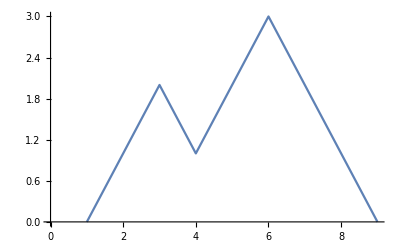
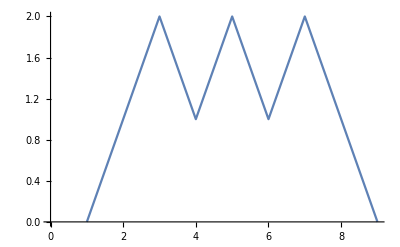
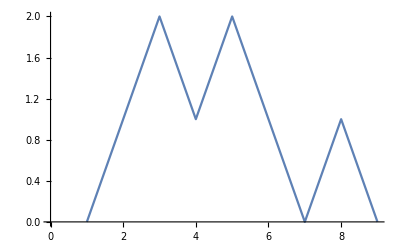
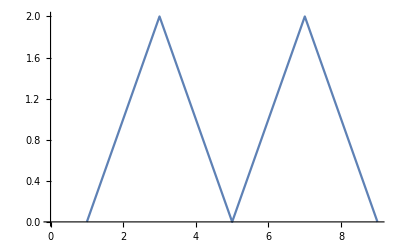

```mathematica
ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,#]/.{0->-1}],0]]&/@Range[0,CatalanNumber[4]-1]
```

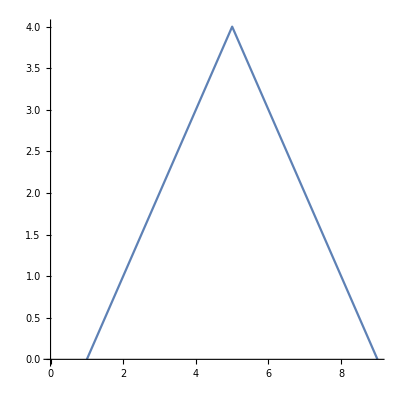
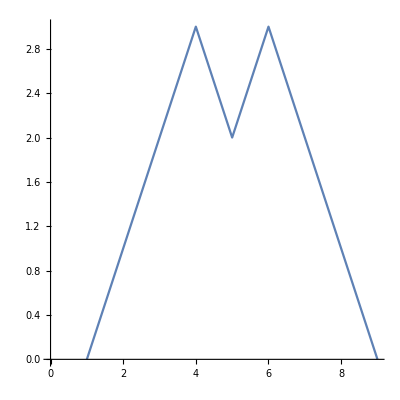
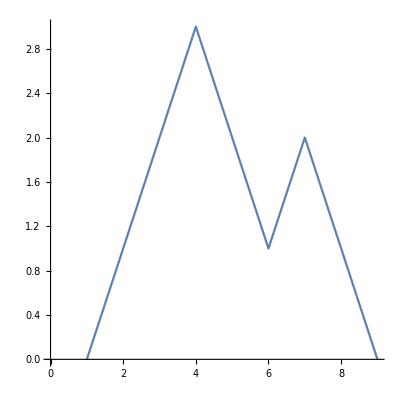
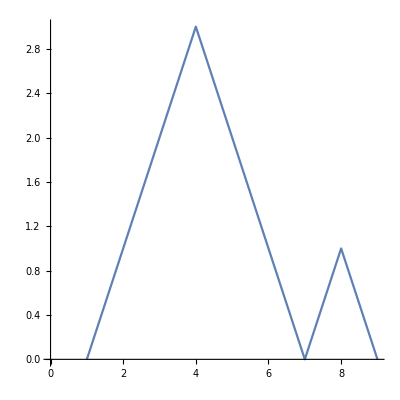
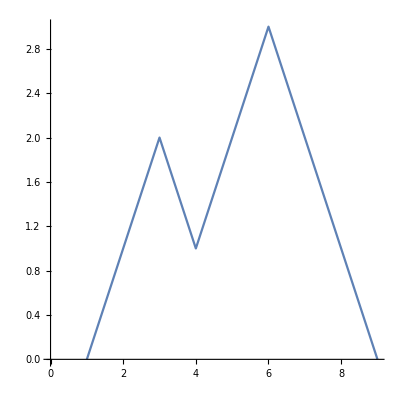
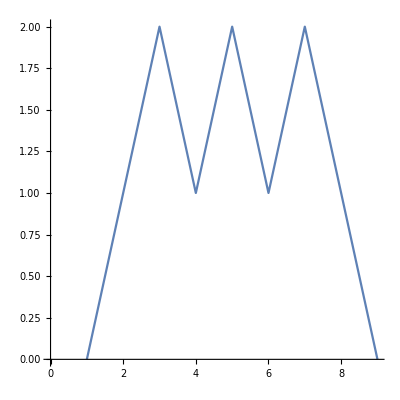
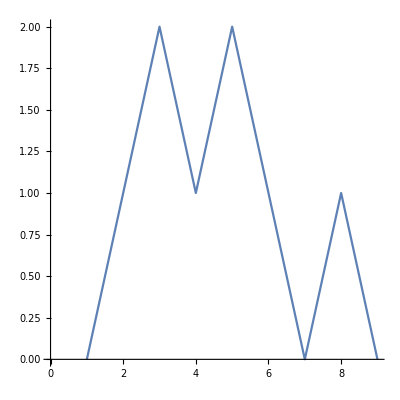
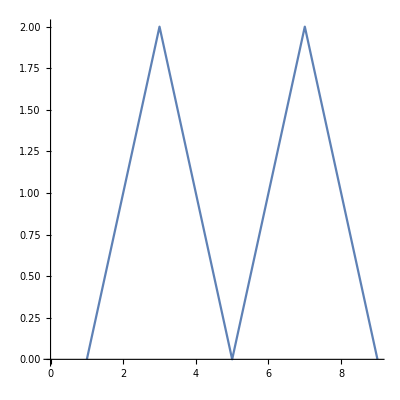

```mathematica
ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[4,#]/.{0->-1}],0],AspectRatio->1]&/@Range[0,CatalanNumber[4]-1]
```

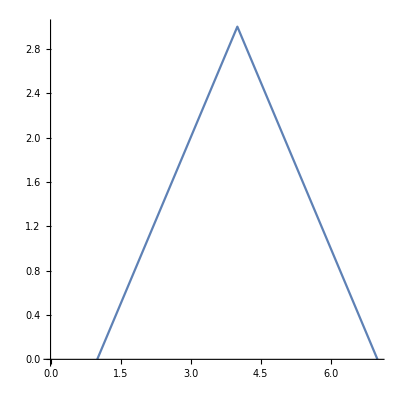
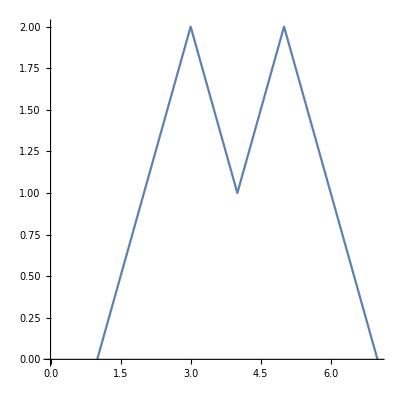
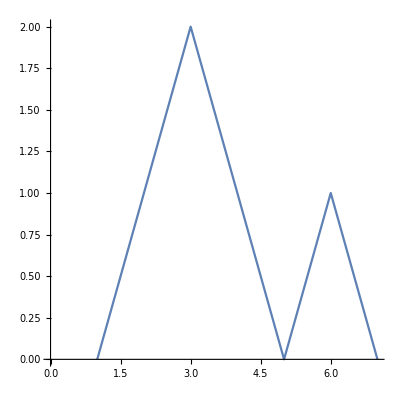
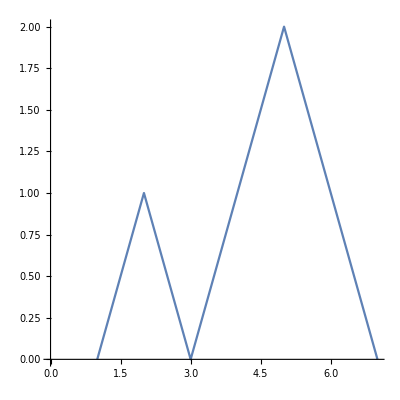
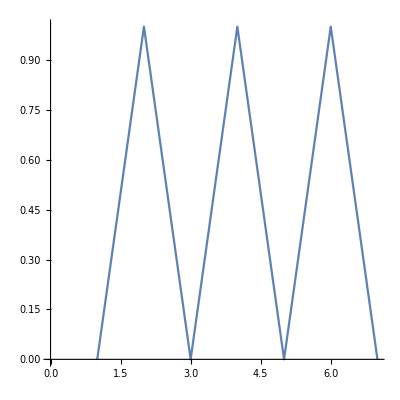

```mathematica
ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[3,#]/.{0->-1}],0],AspectRatio->1]&/@Range[0,CatalanNumber[3]-1]
```

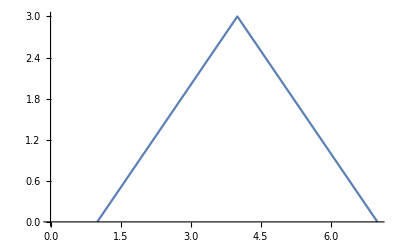
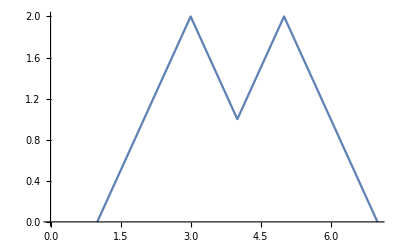
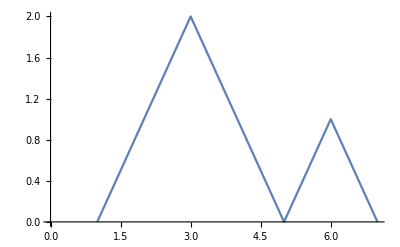
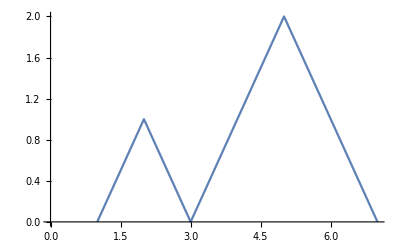
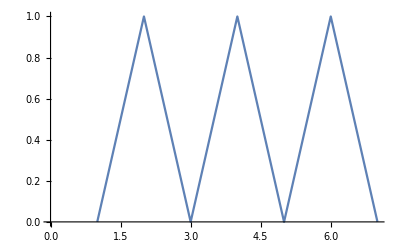

```mathematica
ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[3,#]/.{0->-1}],0],Ticks->None]&/@Range[0,CatalanNumber[3]-1]
```

```mathematica
AbsoluteOptions[-Graphics-]
```

{AlignmentPoint→Center,AspectRatio→0.618034,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0.},AxesStyle→{{},{}},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction→Identity,Epilog→{},FormatType→TraditionalForm,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameStyle→{{{},{}},{{},{}}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle→{{{},{}},{{},{}}},GridLines→None,GridLinesStyle→{{LineColor→GrayLevel[0.5],LineOpacity→0.4,FrontFaceColor→GrayLevel[0.5],BackFaceColor→GrayLevel[0.5],FrontFaceOpacity→0.4,BackFaceOpacity→0.4,GraphicsColor→GrayLevel[0.5],Opacity→0.4,FontColor→GrayLevel[0.5],FontOpacity→0.4},{LineColor→GrayLevel[0.5],LineOpacity→0.4,FrontFaceColor→GrayLevel[0.5],BackFaceColor→GrayLevel[0.5],FrontFaceOpacity→0.4,BackFaceOpacity→0.4,GraphicsColor→GrayLevel[0.5],Opacity→0.4,FontColor→GrayLevel[0.5],FontOpacity→0.4}},ImageMargins→0.,ImagePadding→{{0.5,0.5},{0.5,0.5}},ImageSize→{360.,222.874},ImageSizeRaw→Automatic,LabelStyle→{},Method→{OptimizePlotMarkers→True,OptimizePlotMarkers→True,CoordinatesToolOptions→{DisplayFunction→({Identity[#1⟦1⟧],Identity[#1⟦2⟧]}&),CopiedValueFunction→({Identity[#1⟦1⟧],Identity[#1⟦2⟧]}&)}},PlotLabel→None,PlotRange→{{-2.77556×10^-17,7.},{-1.38778×10^-17,2.}},PlotRangeClipping→True,PlotRangePadding→{{0.145833,0.145833},{0.0430108,0.107527}},PlotRegion→{{0.,1.},{0.,1.}},PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→{{},{}},TicksStyle→{{},{}}}

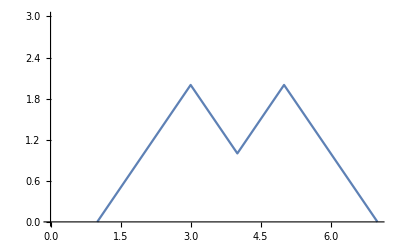
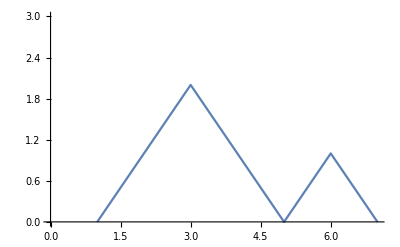
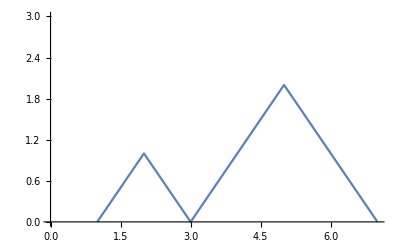
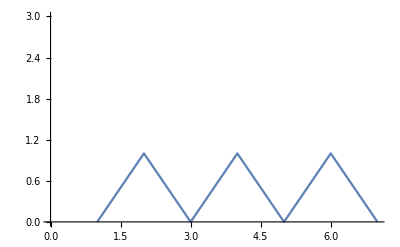
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[3,#]/.{0->-1}],0],Ticks->None,Axes->{True,False},PlotRange->3]&/@Range[0,CatalanNumber[3]-1]
```

```mathematica
First@Range[0,CatalanNumber[3]-1]
```

0

```mathematica
-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[3,0]/.{0->-1}],0]
```

{0,1,2,3,2,1,0}

```mathematica
DyckPaths[n_]:=ListLinePlot[-Prepend[Accumulate[{{-Graphics-, CatalanUnrank}}[n,#]/.{0->-1}],0],Ticks->None,Axes->{True,False},PlotRange->n]&/@Range[0,CatalanNumber[n]-1]
```

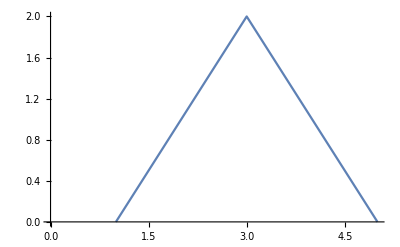
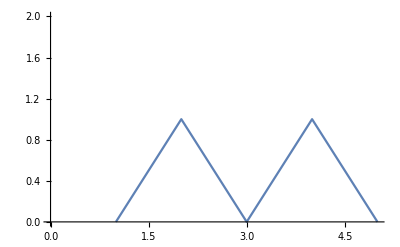

```mathematica
DyckPaths[2]
```

```mathematica
DyckPaths[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

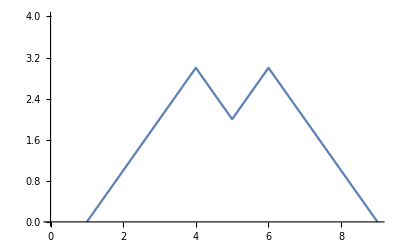
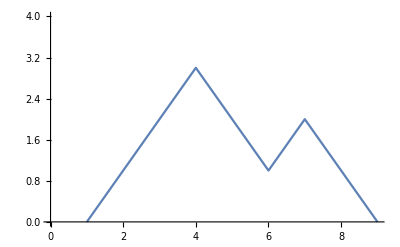
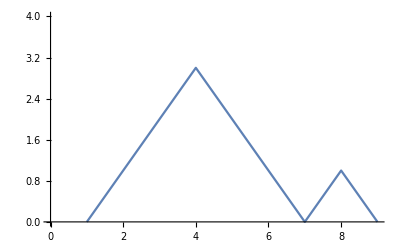
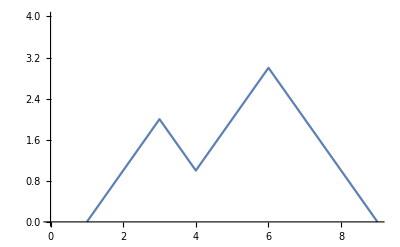
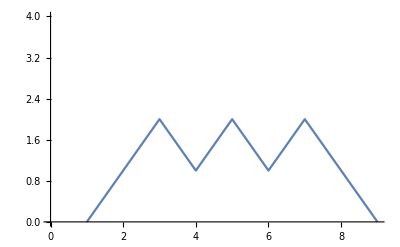
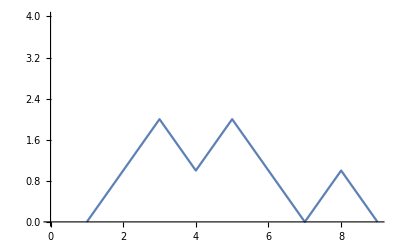
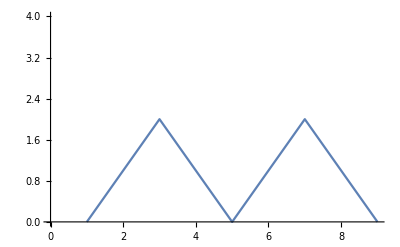
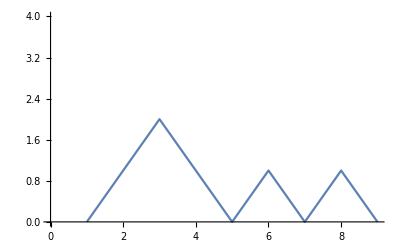
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DyckPaths[4]
```

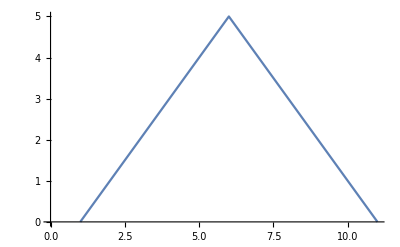
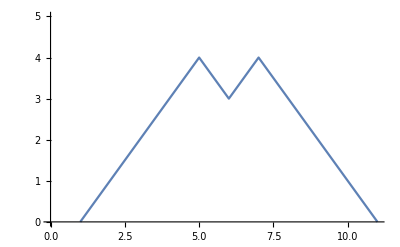
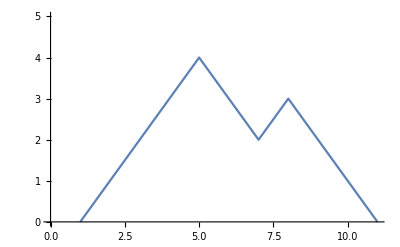
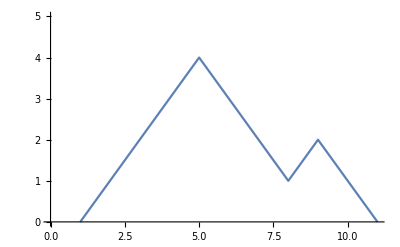
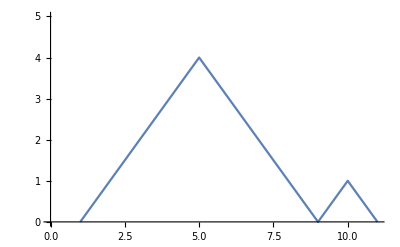
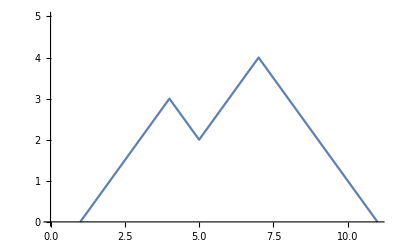
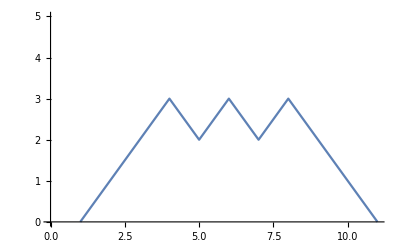
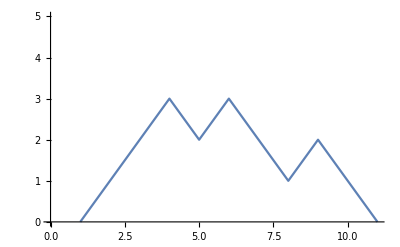

```mathematica
DyckPaths[5]
```

```mathematica
CatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=-1,
lo=lo+m;
y=y-1;
a[[x]]=1],
{x,1,2 n}];
a]
```

```mathematica
CatalanUnrank[3,0]
```

{-1,-1,-1,1,1,1}

```mathematica
-Accumulate[CatalanUnrank[3,0]]
```

{1,2,3,2,1,0}

```mathematica
CatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=-1,
lo=lo+m;
y=y-1;
a[[x]]=1],
{x,1,2 n}];
a]
```

```mathematica
AllPositiveCatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y-1;
a[[x]]=+1,
lo=lo+m;
y=y+1;
a[[x]]=-1],
{x,1,2 n}];
a]
```

```mathematica
AllPositiveCatalanUnrank[3,0]
```

{1,1,-1,1,-1,1}

```mathematica
Accumulate[AllPositiveCatalanUnrank[3,0]]
```

{1,2,1,2,1,2}

```mathematica
CatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=0,
lo=lo+m;
y=y-1;
a[[x]]=1],
{x,1,2 n}];
a]
```

```mathematica
AllPositiveCatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=1,
lo=lo+m;
y=y-1;
a[[x]]=-1],
{x,1,2 n}];
a]
```

```mathematica
AllPositiveCatalanUnrank[3,0]
```

{1,1,1,-1,-1,-1}

```mathematica
Accumulate[AllPositiveCatalanUnrank[3,0]]
```

{1,2,3,2,1,0}

```mathematica
Accumulate[AllPositiveCatalanUnrank[3,1]]
```

{1,2,1,2,1,0}

```mathematica
Prepend[Accumulate[AllPositiveCatalanUnrank[3,1]],0]
```

{0,1,2,1,2,1,0}

```mathematica
Prepend[Accumulate[AllPositiveCatalanUnrank[3,2]],0]
```

{0,1,2,1,0,1,0}

```mathematica
AllPositiveCatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=1,
lo=lo+m;
y=y-1;
a[[x]]=-1],
{x,1,2 n}];
a]
```

```mathematica
DyckPathsUnrankFunction[n_,rank_]:=Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=1,
lo=lo+m;
y=y-1;
a[[x]]=-1],
{x,1,2 n}];
a]
```

```mathematica
DyckPaths[n_]:=ListLinePlot[Prepend[Accumulate[DyckPathsUnrankFunction[n,#]],0],Ticks->None,Axes->{True,False},PlotRange->n]&/@Range[0,CatalanNumber[n]-1]
```

```mathematica
DyckPaths[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DyckPaths[2]
```

{-Graphics-,-Graphics-}

```mathematica
DyckPaths[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Multicolumn[DyckPaths[4]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
GeneratingFunction[CatalanNumber[n],n]
```

GeneratingFunction[CatalanNumber[n],n]

```mathematica
CatalanNumber[Range[10]]
```

{1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
FindGeneratingFunction[CatalanNumber[Range[10]],k]
```

-1/k+2/((1+√(1-4 k)) k)

```mathematica
CountsBy[CatalanNumber[Range[50]],OddQ][True]
```

5

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[50]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
FindGeneratingFunction[CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[50],n]
```

FindGeneratingFunction[{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},n]

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[63]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[62]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[63]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[63]
```

```mathematica
Floor[Log[2,Range[1000]]]
```

{0,1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
Rest[Floor[Log[2,Range[1000]]]]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[1000]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[1000]==Rest[Floor[Log[2,Range[1000]]]]
```

False

```mathematica
Floor[Log[2,Range[1,10]]]
```

{0,1,1,2,2,2,2,3,3,3}

```mathematica
CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[10]
```

{1,1,2,2,2,2,3,3,3,3}

```mathematica
Most[CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[1000]]==Rest[Floor[Log[2,Range[1000]]]]
```

True

```mathematica
Last[Rest[Floor[Log[2,Range[1000]]]]]
```

9

```mathematica
Last[Most[CountsBy[CatalanNumber[Range[#]],OddQ][True]&/@Range[1000]]]
```

9

```mathematica
Last[Rest[Floor[Log[2,Range[1000]]]]]
```

```mathematica
Select[OddQ[CatalanNumber[#]]&][Range[1000,100000]]
```

$Aborted

```mathematica
Length[Select[OddQ[CatalanNumber[#]]&][Range[1000,100000]]]
```

```mathematica
CatalanNumber[1000]
```

2046105521468021692642519982997827217179245642339057975844538099572176010191891863964968026156453752449015750569428595097318163634370154637380666882886375203359653243390929717431080443509007504772912973142253209352126946839844796747697638537600100637918819326569730982083021538057087711176285777909275869648636874856805956580057673173655666887003493944650164153396910927037406301799052584663611016897272893305532116292143271037140718751625839812072682464343153792956281748582435751481498598087586998603921577523657477775758899987954012641033870640665444651660246024318184109046864244732001962029120

```mathematica
Length[Select[OddQ[CatalanNumber[#]]&][Range[1000,1400]]]
```

1

```mathematica
Length[Select[OddQ[CatalanNumber[#]]&][Range[1000,4000]]]
```

2

```mathematica
Length[Select[OddQ[CatalanNumber[#]]&][Range[1000,100000]]]
```

7

How many n are there such that 1000<=n<=100,000 and CatalanNumber[n] is odd?

There are 7.

```mathematica
DyckPathsUnrankFunction//ClearAll
DyckPaths//ClearAll
DyckPathsUnrankFunction[n_,rank_]:=Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=1,
lo=lo+m;
y=y-1;
a[[x]]=-1],
{x,1,2 n}];
a]
DyckPaths[n_,options:OptionsPattern[ListLinePlot]]:=ListLinePlot[Prepend[Accumulate[DyckPathsUnrankFunction[n,#]],0],Ticks->None,Axes->{True,False},PlotRange->n,options]&/@Range[0,CatalanNumber[n]-1]
```

```mathematica
Multicolumn@DyckPaths[5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
?DyckPaths
```

```mathematica
DyckSequences[n_]:=Prepend[Accumulate[DyckPathsUnrankFunction[n,#1]],0]&/@Range[0,CatalanNumber[n]-1]
```

```mathematica
DyckSequences[4]
```

{{0,1,2,3,4,3,2,1,0},{0,1,2,3,2,3,2,1,0},{0,1,2,3,2,1,2,1,0},{0,1,2,3,2,1,0,1,0},{0,1,2,1,2,3,2,1,0},{0,1,2,1,2,1,2,1,0},{0,1,2,1,2,1,0,1,0},{0,1,2,1,0,1,2,1,0},{0,1,2,1,0,1,0,1,0},{0,1,0,1,2,3,2,1,0},{0,1,0,1,2,1,2,1,0},{0,1,0,1,2,1,0,1,0},{0,1,0,1,0,1,2,1,0},{0,1,0,1,0,1,0,1,0}}

```mathematica
ListLinePlot[Range[0,4],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[-Range[0,4],PlotRange->All]
```

-Graphics-

```mathematica
DyckSequence//ClearAll
DyckSequence[n_,rank_]:=Prepend[Accumulate[DyckPathsUnrankFunction[n,rank]],0]
```

```mathematica
DyckSequence[3,0]
```

{0,1,2,3,2,1,0}

```mathematica
?DyckPathsUnrankFunction
```

```mathematica
Transpose[{DyckSequence[3,0],Range[0,CatalanNumber[3]+1]}]
```

{{0,0},{1,1},{2,2},{3,3},{2,4},{1,5},{0,6}}

```mathematica
ListLinePlot[Transpose[{DyckSequence[3,0],Range[0,CatalanNumber[3]+1]}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{DyckSequence[3,4],Range[0,CatalanNumber[3]+1]}]]
```

-Graphics-

```mathematica
ListLinePlot[{{0,0},{1,0},{1,-1}}]
```

-Graphics-

```mathematica
ListLinePlot[{{0,0},{1,0},{1,-1},{1,-2}}]
```

-Graphics-

```mathematica
ListLinePlot[{{0,0},{1,0},{1,-1},{1,-2},{2,-2}}]
```

-Graphics-

```mathematica
ListLinePlot[{{0,0},{0,-1},{1,-1},{1,-2},{2,-2}}]
```

-Graphics-

```mathematica
Transpose[{{0,0},{0,-1},{1,-1},{1,-2},{2,-2}}]
```

{{0,0,1,1,2},{0,-1,-1,-2,-2}}

```mathematica
-Transpose[{{0,0},{0,-1},{1,-1},{1,-2},{2,-2}}]
```

{{0,0,-1,-1,-2},{0,1,1,2,2}}

```mathematica
DyckSequences[3]
```

{{0,1,2,3,2,1,0},{0,1,2,1,2,1,0},{0,1,2,1,0,1,0},{0,1,0,1,2,1,0},{0,1,0,1,0,1,0}}

```mathematica
First[DyckSequences[3]]
```

{0,1,2,3,2,1,0}

```mathematica
ResourceFunction["CatalanUnrank"][5,#]&/@Range[0,CatalanNumber[5]-1]
```

{{0,0,0,0,0,1,1,1,1,1},{0,0,0,0,1,0,1,1,1,1},{0,0,0,0,1,1,0,1,1,1},{0,0,0,0,1,1,1,0,1,1},{0,0,0,0,1,1,1,1,0,1},{0,0,0,1,0,0,1,1,1,1},{0,0,0,1,0,1,0,1,1,1},{0,0,0,1,0,1,1,0,1,1},{0,0,0,1,0,1,1,1,0,1},{0,0,0,1,1,0,0,1,1,1},{0,0,0,1,1,0,1,0,1,1},{0,0,0,1,1,0,1,1,0,1},{0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,1,0,1,0,1},{0,0,1,0,0,0,1,1,1,1},{0,0,1,0,0,1,0,1,1,1},{0,0,1,0,0,1,1,0,1,1},{0,0,1,0,0,1,1,1,0,1},{0,0,1,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,0,1,1},{0,0,1,0,1,0,1,1,0,1},{0,0,1,0,1,1,0,0,1,1},{0,0,1,0,1,1,0,1,0,1},{0,0,1,1,0,0,0,1,1,1},{0,0,1,1,0,0,1,0,1,1},{0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,1,0,0,1,1},{0,0,1,1,0,1,0,1,0,1},{0,1,0,0,0,0,1,1,1,1},{0,1,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,1,0,1,1},{0,1,0,0,0,1,1,1,0,1},{0,1,0,0,1,0,0,1,1,1},{0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,1,0,0,1,1},{0,1,0,0,1,1,0,1,0,1},{0,1,0,1,0,0,0,1,1,1},{0,1,0,1,0,0,1,0,1,1},{0,1,0,1,0,0,1,1,0,1},{0,1,0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1}}

```mathematica
RandomChoice[ResourceFunction["CatalanUnrank"][5,#]&/@Range[0,CatalanNumber[5]-1]]
```

{0,0,1,0,1,1,0,0,1,1}

```mathematica
{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}
```

{{0,-1},{0,-1},{1,0},{0,-1},{1,0},{1,0},{0,-1},{0,-1},{1,0},{1,0}}

```mathematica
Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}]
```

{{0,-1},{0,-2},{1,-2},{1,-3},{2,-3},{3,-3},{3,-4},{3,-5},{4,-5},{5,-5}}

```mathematica
Prepend[Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}],{0,0}]
```

{{0,0},{0,-1},{0,-2},{1,-2},{1,-3},{2,-3},{3,-3},{3,-4},{3,-5},{4,-5},{5,-5}}

```mathematica
ListLinePlot[Prepend[Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}],{0,0}]]
```

-Graphics-

```mathematica
Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}]
```

{{0,-1},{0,-2},{1,-2},{1,-3},{2,-3},{3,-3},{3,-4},{3,-5},{4,-5},{5,-5}}

```mathematica
-Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}]
```

{{0,1},{0,2},{-1,2},{-1,3},{-2,3},{-3,3},{-3,4},{-3,5},{-4,5},{-5,5}}

```mathematica
Reverse/@-Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}]
```

{{1,0},{2,0},{2,-1},{3,-1},{3,-2},{3,-3},{4,-3},{5,-3},{5,-4},{5,-5}}

```mathematica
ListLinePlot[Reverse/@-Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}]]
```

-Graphics-

```mathematica
RandomChoice[ResourceFunction["CatalanUnrank"][5,#]&/@Range[0,CatalanNumber[5]-1]]
```

{0,1,0,0,0,0,1,1,1,1}

```mathematica
ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}]]&/@(ResourceFunction["CatalanUnrank"][5,#]&/@Range[0,CatalanNumber[5]-1])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WalksAboveTheDiagonal[n_]:=ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}]]&/@(ResourceFunction["CatalanUnrank"][n,#]&/@Range[0,CatalanNumber[n]-1])
```

```mathematica
WalksAboveTheDiagonal[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?DyckPaths
```

```mathematica
WalksAboveTheDiagonal[n_,options:OptionsPattern[ListLinePlot]]:=(ListLinePlot[Prepend[Accumulate[DyckPathsUnrankFunction[n,#1]],0],Ticks->None,Axes->{True,False},PlotRange->n,options]&)/@Range[0,CatalanNumber[n]-1]
```

```mathematica
WalksAboveTheDiagonal[n_]:=ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}]]&/@(ResourceFunction["CatalanUnrank"][n,#]&/@Range[0,CatalanNumber[n]-1])
```

```mathematica
ClearAll[WalksAboveTheDiagonal]
WalksAboveTheDiagonal[m_,options:OptionsPattern[ListLinePlot]]:=ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}],Ticks->None,Axes->{True,False},options]&/@(CatalanUnrank[m,#]&/@Range[0,CatalanNumber[m]-1])
```

```mathematica
?WalksAboveTheDiagonal
```

```mathematica
WalksAboveTheDiagonal//ClearAll
WalksAboveTheDiagonal[n_]:=ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}]]&/@(CatalanUnrank[n,#]&/@Range[0,CatalanNumber[n]-1])
```

```mathematica
WalksAboveTheDiagonal[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### walks above the diagonal

```mathematica
WalksAboveTheDiagonal//ClearAll
WalksAboveTheDiagonal[n_]:=ListLinePlot[Reverse/@-Accumulate[#/.{0->{0,-1},1->{1,0}}],Ticks->None]&/@(ResourceFunction["CatalanUnrank"][n,#]&/@Range[0,CatalanNumber[n]-1])
```

```mathematica
WalksAboveTheDiagonal[2]
```

{-Graphics-,-Graphics-}

```mathematica
WalksAboveTheDiagonal[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WalksAboveTheDiagonal[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[WalksAboveTheDiagonal[4]]
```

14

```mathematica
CatalanNumber[4]
```

14

```mathematica
WalksAboveTheDiagonal[5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[{Prepend[Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}],{0,0}],Transpose[{Range[0,5],Range[0,-5,-1]}]}]
```

-Graphics-

```mathematica
ListLinePlot[{Reverse/@-Prepend[Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}],{0,0}],Transpose[{Range[0,5],Range[0,-5,-1]}]}]
```

-Graphics-

```mathematica
ListLinePlot[{Reverse/@-Prepend[Accumulate[{0,0,1,0,1,1,0,0,1,1}/.{0->{0,-1},1->{1,0}}],{0,0}],Transpose[{Range[0,5],Range[0,-5,-1]}]}]
```

-Graphics-

```mathematica
(-CatalanUnrank[5,#]/.{0->{0,-1},1->{1,0}})&/@Range[0,CatalanNumber[5]-1]
```

{{{1,0},{1,0},{1,0},{1,0},{1,0},-1,-1,-1,-1,-1},{{1,0},{1,0},{1,0},{1,0},-1,{1,0},-1,-1,-1,-1},{{1,0},{1,0},{1,0},{1,0},-1,-1,{1,0},-1,-1,-1},{{1,0},{1,0},{1,0},{1,0},-1,-1,-1,{1,0},-1,-1},{{1,0},{1,0},{1,0},{1,0},-1,-1,-1,-1,{1,0},-1},{{1,0},{1,0},{1,0},-1,{1,0},{1,0},-1,-1,-1,-1},{{1,0},{1,0},{1,0},-1,{1,0},-1,{1,0},-1,-1,-1},{{1,0},{1,0},{1,0},-1,{1,0},-1,-1,{1,0},-1,-1},{{1,0},{1,0},{1,0},-1,{1,0},-1,-1,-1,{1,0},-1},{{1,0},{1,0},{1,0},-1,-1,{1,0},{1,0},-1,-1,-1},{{1,0},{1,0},{1,0},-1,-1,{1,0},-1,{1,0},-1,-1},{{1,0},{1,0},{1,0},-1,-1,{1,0},-1,-1,{1,0},-1},{{1,0},{1,0},{1,0},-1,-1,-1,{1,0},{1,0},-1,-1},{{1,0},{1,0},{1,0},-1,-1,-1,{1,0},-1,{1,0},-1},{{1,0},{1,0},-1,{1,0},{1,0},{1,0},-1,-1,-1,-1},{{1,0},{1,0},-1,{1,0},{1,0},-1,{1,0},-1,-1,-1},{{1,0},{1,0},-1,{1,0},{1,0},-1,-1,{1,0},-1,-1},{{1,0},{1,0},-1,{1,0},{1,0},-1,-1,-1,{1,0},-1},{{1,0},{1,0},-1,{1,0},-1,{1,0},{1,0},-1,-1,-1},{{1,0},{1,0},-1,{1,0},-1,{1,0},-1,{1,0},-1,-1},{{1,0},{1,0},-1,{1,0},-1,{1,0},-1,-1,{1,0},-1},{{1,0},{1,0},-1,{1,0},-1,-1,{1,0},{1,0},-1,-1},{{1,0},{1,0},-1,{1,0},-1,-1,{1,0},-1,{1,0},-1},{{1,0},{1,0},-1,-1,{1,0},{1,0},{1,0},-1,-1,-1},{{1,0},{1,0},-1,-1,{1,0},{1,0},-1,{1,0},-1,-1},{{1,0},{1,0},-1,-1,{1,0},{1,0},-1,-1,{1,0},-1},{{1,0},{1,0},-1,-1,{1,0},-1,{1,0},{1,0},-1,-1},{{1,0},{1,0},-1,-1,{1,0},-1,{1,0},-1,{1,0},-1},{{1,0},-1,{1,0},{1,0},{1,0},{1,0},-1,-1,-1,-1},{{1,0},-1,{1,0},{1,0},{1,0},-1,{1,0},-1,-1,-1},{{1,0},-1,{1,0},{1,0},{1,0},-1,-1,{1,0},-1,-1},{{1,0},-1,{1,0},{1,0},{1,0},-1,-1,-1,{1,0},-1},{{1,0},-1,{1,0},{1,0},-1,{1,0},{1,0},-1,-1,-1},{{1,0},-1,{1,0},{1,0},-1,{1,0},-1,{1,0},-1,-1},{{1,0},-1,{1,0},{1,0},-1,{1,0},-1,-1,{1,0},-1},{{1,0},-1,{1,0},{1,0},-1,-1,{1,0},{1,0},-1,-1},{{1,0},-1,{1,0},{1,0},-1,-1,{1,0},-1,{1,0},-1},{{1,0},-1,{1,0},-1,{1,0},{1,0},{1,0},-1,-1,-1},{{1,0},-1,{1,0},-1,{1,0},{1,0},-1,{1,0},-1,-1},{{1,0},-1,{1,0},-1,{1,0},{1,0},-1,-1,{1,0},-1},{{1,0},-1,{1,0},-1,{1,0},-1,{1,0},{1,0},-1,-1},{{1,0},-1,{1,0},-1,{1,0},-1,{1,0},-1,{1,0},-1}}

```mathematica
Accumulate[(-CatalanUnrank[5,#]/.{0->{0,-1},1->{1,0}})]&/@Range[0,CatalanNumber[5]-1]
```

{{{1,0},{2,0},{3,0},{4,0},{5,0},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{4,0},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{3,0},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{2,0},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}}}

```mathematica
Prepend[Accumulate[(-CatalanUnrank[5,#]/.{0->{0,-1},1->{1,0}})],{0,0}]&/@Range[0,CatalanNumber[5]-1]
```

{{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{4,0},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{4,0},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{3,0},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{2,0},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{4,-1},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{3,-1},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{2,-1},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{3,-2},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{2,-2},{1,-3},{0,-4},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{2,-3},{1,-4},{0,-5}},{{0,0},{1,0},{0,-1},{1,-1},{0,-2},{1,-2},{0,-3},{1,-3},{0,-4},{1,-4},{0,-5}}}

```mathematica
ListLinePlot[{Prepend[Accumulate[(-CatalanUnrank[5,#]/.{-1->{0,-1},1->{1,0}})],{0,0}],Transpose[{Range[0,5],Range[0,-5,-1]}]}]&/@Range[0,CatalanNumber[5]-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[{Prepend[Accumulate[(CatalanUnrank[5,#]/.{-1->{0,-1},1->{1,0}})],{0,0}],Transpose[{Range[0,5],Range[0,-5,-1]}]}]&/@Range[0,CatalanNumber[5]-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WalksBelowTheDiagonal[n_]:=ListLinePlot[{Prepend[Accumulate[(CatalanUnrank[n,#]/.{-1->{0,-1},1->{1,0}})],{0,0}],Transpose[{Range[0,n],Range[0,-n,-1]}]},Ticks->None]&/@Range[0,CatalanNumber[n]-1]
```

```mathematica
WalksBelowTheDiagonal[2]
```

{-Graphics-,-Graphics-}

```mathematica
WalksBelowTheDiagonal[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WalksAboveTheDiagonal[n_]:=ListLinePlot[{Prepend[Accumulate[(-CatalanUnrank[n,#]/.{-1->{0,-1},1->{1,0}})],{0,0}],Transpose[{Range[0,n],Range[0,-n,-1]}]},Ticks->None]&/@Range[0,CatalanNumber[n]-1]
```

```mathematica
WalksAboveTheDiagonal[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[n_]:=Flatten[(sign↦ListLinePlot[{Prepend[Accumulate[(sign CatalanUnrank[n,#]/.{-1->{0,-1},1->{1,0}})],{0,0}],Transpose[{Range[0,n],Range[0,-n,-1]}]},Ticks->None]&/@Range[0,CatalanNumber[n]-1])/@{1,-1}]
```

```mathematica
AllWalksAboveOrBelowTheDiagonal[3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[3]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[4]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[5]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_]:=Flatten[(sign↦ListLinePlot[{Prepend[Accumulate[(sign CatalanUnrank[n,#]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}})],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None]&/@Range[0,CatalanNumber[n]-1])/@{1,-1}]
```

```mathematica
AllWalksAboveOrBelowTheDiagonal[3,1,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[3,-1,-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[3,-1,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[3,1,-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal//ClearAll
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_,options:OptionsPattern[ListLinePlot]]:=Flatten[(sign↦ListLinePlot[{Prepend[Accumulate[(sign CatalanUnrank[n,#]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}})],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None,options]&/@Range[0,CatalanNumber[n]-1])/@{1,-1}]
```

```mathematica
AllWalksAboveOrBelowTheDiagonal[3,1,1,Filling->Axis]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[3,1,1,Filling->Axis]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
?AllWalksAboveOrBelowTheDiagonal
```

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[4,1,1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[4,1,-1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[4,-1,-1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[4,-1,1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[6,-1,1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[AllWalksAboveOrBelowTheDiagonal[7,1,1]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
?AllWalksAboveOrBelowTheDiagonal
```

```mathematica
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_,"WalkType"->All,options:OptionsPattern[ListLinePlot]]:=Flatten[Function[sign,(ListLinePlot[{Prepend[Accumulate[sign CatalanUnrank[n,#1]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}}],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None,options]&)/@Range[0,CatalanNumber[n]-1]]/@{1,-1}]
```

```mathematica
AllWalksAboveOrBelowTheDiagonal//ClearAll
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_,options:OptionsPattern[ListLinePlot]]:=Flatten[Function[sign,(ListLinePlot[{Prepend[Accumulate[sign CatalanUnrank[n,#1]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}}],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None,options]&)/@Range[0,CatalanNumber[n]-1]]/@{1,-1}]
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_,"WalkType"->All,options:OptionsPattern[ListLinePlot]]:=Flatten[Function[sign,(ListLinePlot[{Prepend[Accumulate[sign CatalanUnrank[n,#1]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}}],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None,options]&)/@Range[0,CatalanNumber[n]-1]]/@{1,-1}]
AllWalksAboveOrBelowTheDiagonal[n_,horizontaldirectionsign_,verticaldirectionsign_,"Below",options:OptionsPattern[ListLinePlot]]:=Flatten[Function[sign,(ListLinePlot[{Prepend[Accumulate[sign CatalanUnrank[n,#1]/.{-1->{0,horizontaldirectionsign},1->{verticaldirectionsign,0}}],{0,0}],Transpose[{verticaldirectionsign Range[0,n],horizontaldirectionsign Range[0,n]}]},Ticks->None,options]&)/@Range[0,CatalanNumber[n]-1]]/@{-1}]
```

```mathematica
AllWalksAboveOrBelowTheDiagonal[4,1,1,"Below"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[4,1,-1,"Below"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[4,-1,1,"Below"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AllWalksAboveOrBelowTheDiagonal[4,-1,-1,"Below"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}